## Exploring autocorrelation in the data

```mathematica
data=Table[RandomReal[{-1,1}],{i,1,500}];
```

```mathematica
corrdata=Table[Sin[RandomReal[{-5,5}]],{i,1,500}];
```

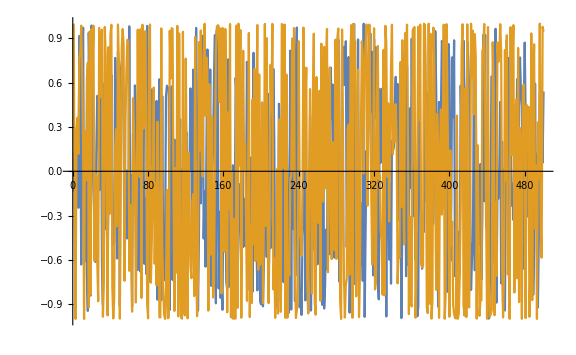

```mathematica
ListLinePlot[{data,corrdata},ImageSize->Large]
```

```mathematica
AutocorrelationFunction[dat_,τ_]:=1/Length[dat] Sum[(dat[[i]]-Mean[dat])*(dat[[i+τ]]-Mean[dat]),{i,1,Length[dat]-τ}]/Variance[dat]
```

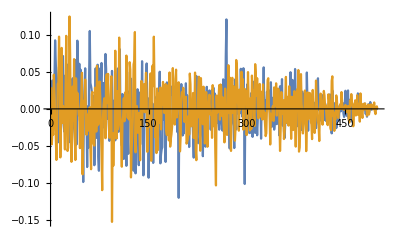

```mathematica
ListLinePlot[{Table[AutocorrelationFunction[data,τ],{τ,1,Length[corrdata]}],Table[AutocorrelationFunction[corrdata,τ],{τ,1,Length[corrdata]}]},PlotRange->Full]
```

```mathematica
BlockAvList[dat_,block_]:=Table[Mean[Table[dat[[i+j]],{j,0,block-1}]],{i,1, Length[dat]-block,block}]
```

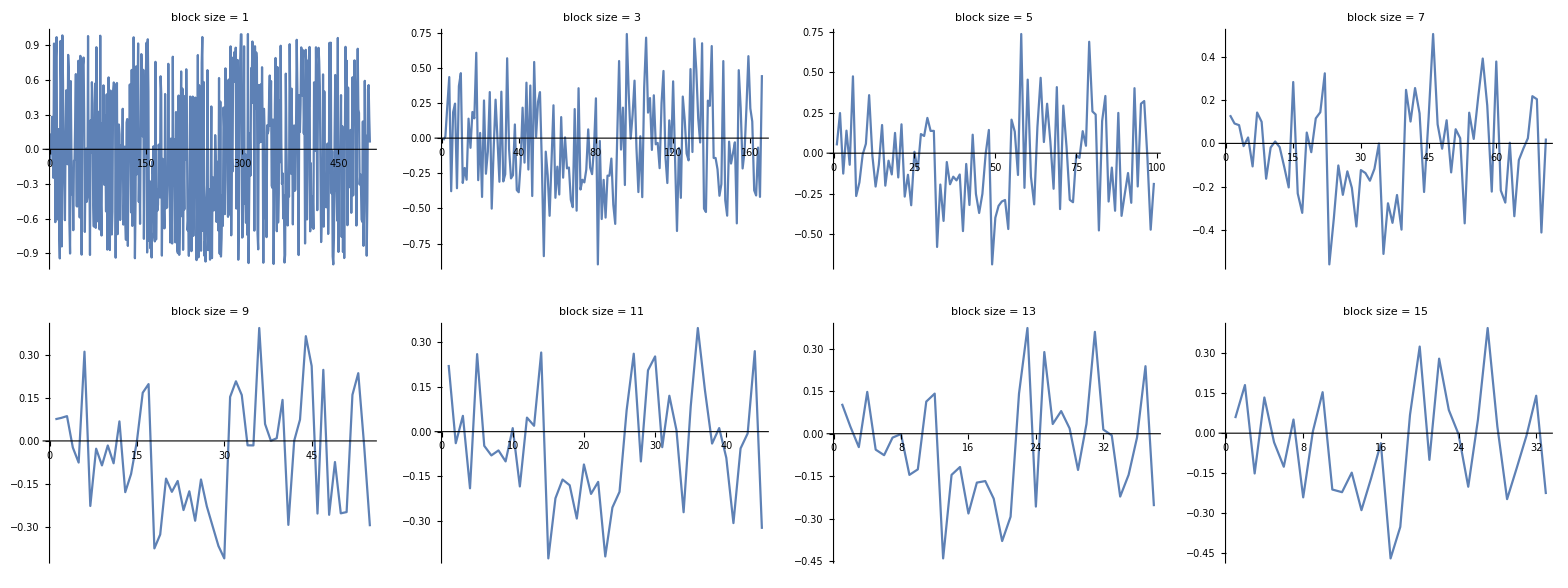

```mathematica
Grid[Partition[Table[ListLinePlot[BlockAvList[data,i],PlotLabel->StringJoin["block size = ",ToString[i]]],{i,1,20,2}],4]]
```

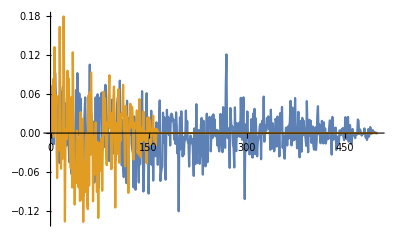

```mathematica
ListLinePlot[{Table[AutocorrelationFunction[data,τ],{τ,1,Length[corrdata]}],Table[AutocorrelationFunction[BlockAvList[data,3],τ],{τ,1,Length[corrdata]}]},PlotRange->Full]
```

```mathematica
ListLinePlot[Table[Table[i*.2+AutocorrelationFunction[BlockAvList[data,i],τ],{τ,1,Length[data]}],{i,1,20,2}],PlotRange->Full,ImageSize->Large,PlotLabels->Table[StringJoin["block size = ",ToString[i]],{i,1,20,2}]]
```

-Graphics-

## Block averaging

```mathematica
Av=Mean[data]
```

-0.0387171

```mathematica
MovAv[dat_,block_]:=Mean[MovingAverage[dat,block]]
```

```mathematica
BlockAv[dat_,block_]:=Mean[Table[Mean[Table[dat[[i+j]],{j,0,block-1}]],{i,1, Length[dat]-block,block}]]
```

```mathematica
VarBlockAv[dat_,block_]:=Total[
Table[
Mean[
Table[dat[[i+j]]^2,{j,0,block-1}]
]-Mean[
Table[dat[[i+j]],{j,0,block-1}]
]^2
,{i,1, Length[dat]-block,block}]/(Length[dat]/block-1)]
```

```mathematica
StdBlockAv[dat_,block_]:=Sqrt[VarBlockAv[dat,block]/block]
```

```mathematica
ListLinePlot[{Table[BlockAv[data,n],{n,1,200}],Table[MovAv[data,n],{n,1,200}],Table[Mean[data],{n,1,200}]},ImageSize->Large,PlotLabel->"uncorrelated data",PlotLabels->{"Block Average","Moving Average","Mean"},PlotStyle->{RGBColor[1, 0.6900000000000001, 0.33],RGBColor[0.39, 0.54, 0.73],RGBColor[0.9, 0.39, 0.45]}]
```

-Graphics-

```mathematica
ListLinePlot[{Table[BlockAv[corrdata,n],{n,1,200}],Table[MovAv[corrdata,n],{n,1,200}],Table[Mean[corrdata],{n,1,200}]},ImageSize->Large,PlotLabel->"correlated data",PlotLabels->{"Block Average","Moving Average","Mean"},PlotStyle->{RGBColor[1, 0.6900000000000001, 0.33],RGBColor[0.39, 0.54, 0.73],RGBColor[0.9, 0.39, 0.45]},PlotRange->Full]
```

-Graphics-

## Error bars

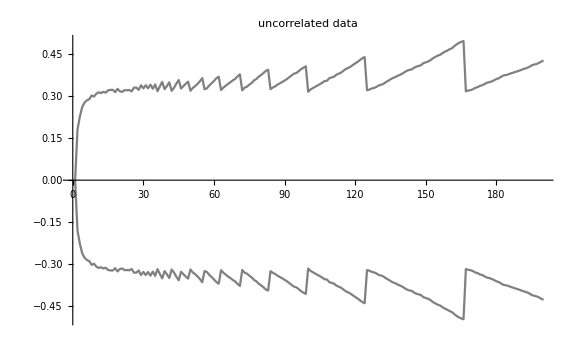

```mathematica
ListLinePlot[{Table[VarBlockAv[data,n],{n,1,200}],-Table[VarBlockAv[data,n],{n,1,200}]},PlotLabel->"uncorrelated data",PlotStyle->Gray]
```

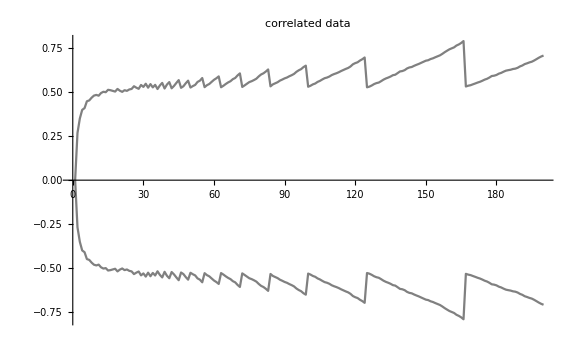

```mathematica
ListLinePlot[{Table[VarBlockAv[corrdata,n],{n,1,200}],-Table[VarBlockAv[corrdata,n],{n,1,200}]},PlotLabel->"correlated data",PlotStyle->Gray]
```

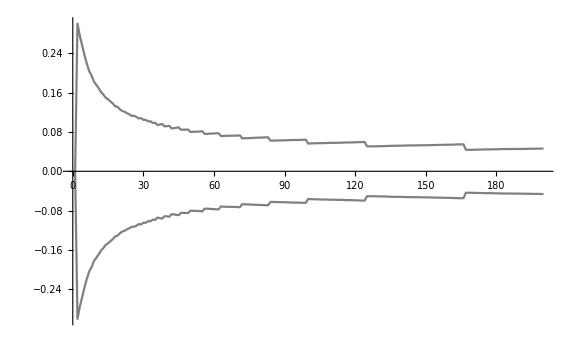

```mathematica
ListLinePlot[{Table[StdBlockAv[data,n],{n,1,200}],-Table[StdBlockAv[data,n],{n,1,200}]},PlotStyle->Gray]
```

```mathematica
Needs["ErrorBarPlots`"]
```

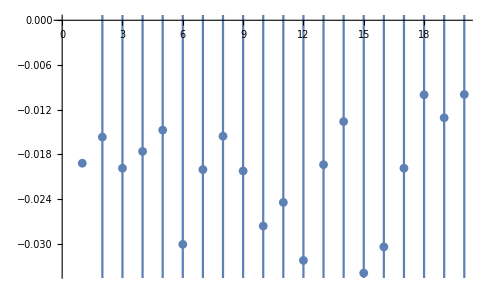

```mathematica
ErrorListPlot[Transpose[{Table[BlockAv[corrdata,n],{n,1,200,10}],Table[StdBlockAv[corrdata,n],{n,1,200,10}]}],PlotRange->Automatic]
```

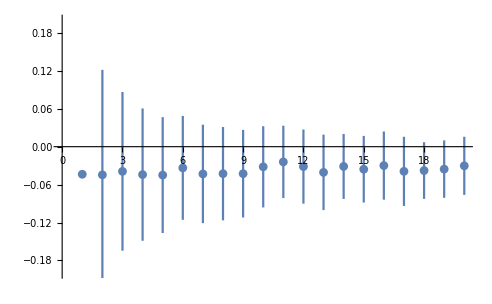

```mathematica
ErrorListPlot[Transpose[{Table[BlockAv[data,n],{n,1,200,10}],Table[StdBlockAv[data,n],{n,1,200,10}]}],PlotRange->{-.2,.2}]
```